Problem 1

This is trivially solvable, there is just the need of performing the plots needed, and goes as follows.

```mathematica
IXY1[θ_]:=1/2 (2-Log2[1/2 (1-Sin[θ])] (-1+Sin[θ])+Log2[1/2 (1+Sin[θ])] (1+Sin[θ]));
```

```mathematica
IXB1[θ_]:=-Cos[θ/2]^2Log2[Cos[θ/2]^2]-Sin[θ/2]^2Log2[Sin[θ/2]^2];
```

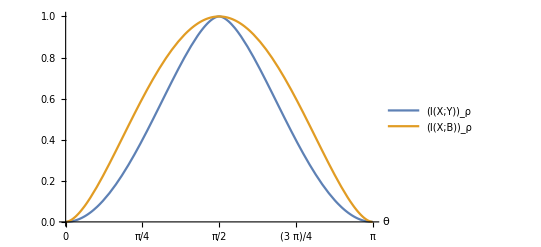

```mathematica
Plot[{IXY1[x],IXB[x]},{x,0,Pi}, PlotLegends->{Subscript["I(X;Y)","ρ"],Subscript["I(X;B)","ρ"]},AxesLabel->{Style[θ, Medium]}, Ticks->{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}]
```

```mathematica
Export["Exercice1.pdf",%]
```

Exercice1.pdf

Problem 2

Definition of the basis

Here the basic vectors needed to perform the computations are defined.

```mathematica
T0[θ_]:=({{N[Cos[θ/2]]}, {N[Sin[θ/2]]}});
T1[θ_]:=({{N[Cos[θ/2]]}, {-N[Sin[θ/2]]}});
```

```mathematica
ψ0[θ_]:=KroneckerProduct[T0[θ],T0[θ],T0[θ]];
ψ1[θ_]:=KroneckerProduct[T0[θ],T1[θ], T1[θ]];
ψ2[θ_]:=KroneckerProduct[T1[θ],T0[θ], T1[θ]];
ψ3[θ_]:=KroneckerProduct[T1[θ],T1[θ], T0[θ]];
```

```mathematica
ψ[θ_]:=List[ψ0[θ],ψ1[θ],ψ2[θ],ψ3[θ]];
ψT[θ_]:={Transpose[ψ0[θ]],Transpose[ψ1[θ]],Transpose[ψ2[θ]],Transpose[ψ3[θ]]};
```

```mathematica
k={({{1}, {0}, {0}, {0}}),({{0}, {1}, {0}, {0}}),({{0}, {0}, {1}, {0}}),({{0}, {0}, {0}, {1}})};
```

As well as the probability distribution of X

```mathematica
px={1/4,1/4,1/4,1/4};
```

Definition of the initial state

```mathematica
ρXB3[θ_]:=Sum[px[[i]]*KroneckerProduct[k[[i]].Transpose[k[[i]]],ψ[θ][[i]].ψT[θ][[i]]],{i,1,4}];
```

```mathematica
ρB3[θ_]:=1/4*Sum[ψ[θ][[i]].ψT[θ][[i]],{i,1,4}];
```

Definition of the POVM

First the ρ^{-1/2} is defined using the pseudo-inverse as it is non invertible

```mathematica
ρsqrt[θ_]:=PseudoInverse[MatrixPower[ρB3[θ],1/2]]
```

Then the POVM can be defined as follows, where Λ is a vector in which in each component represents one of the outputs of the POVM appears

```mathematica
Λ[θ_]:=1/4*{ρsqrt[θ].ψ0[θ].ψT[θ][[1]].ρsqrt[θ],ρsqrt[θ].ψ1[θ].ψT[θ][[2]].ρsqrt[θ],ρsqrt[θ].ψ2[θ].ψT[θ][[3]].ρsqrt[θ],ρsqrt[θ].ψ3[θ].ψT[θ][[4]].ρsqrt[θ]};
```

Definition of the Post-channel state, directly through the eigenvalues

Let first define a function that accounts for every P(y|x;θ).

```mathematica
F[x_,y_,θ_]:=((ψT[θ][[x]].Λ[θ][[y]].ψ[θ][[x]])[[1]])[[1]];
```

Then let us define the ρ_{y|x} through its eigenvalues, where each array accounts for ρ_{y|x=i}. This is then a matrig of de form  ρ_{y|x} =Diag[ρ_{y|x=1},ρ_{y|x=2},ρ_{y|x=3},ρ_{y|x=4}]

```mathematica
ρYcondX[θ_]:=Array[F[1,##,θ]&,4]~Join~Array[F[2,##,θ]&,4]~Join~Array[F[3,##,θ]&,4]~Join~Array[F[4,##,θ]&,4];
```

From the previous matrix it is easy to find ρ_Y as we just need to add every element from the previous matrix with y=y’.

```mathematica
ρY[θ_]:=1/4 {ρYcondX[θ][[1]]+ρYcondX[θ][[5]]+ρYcondX[θ][[9]]+ρYcondX[θ][[13]],ρYcondX[θ][[2]]+ρYcondX[θ][[6]]+ρYcondX[θ][[10]]+ρYcondX[θ][[14]],ρYcondX[θ][[3]]+ρYcondX[θ][[7]]+ρYcondX[θ][[11]]+ρYcondX[θ][[15]],ρYcondX[θ][[4]]+ρYcondX[θ][[8]]+ρYcondX[θ][[12]]+ρYcondX[θ][[16]]};
```

Computation of the mutual informations

Now using I(X;Y)=H(Y)-H(Y|X), I(X;B)=H(B)-H(B|X)=H(B):

First the function that finds the eigenvalue for the first state is implemented, applying a Select function which allows for the elimination of errors coming from ill-defined numbers (that usually result in negative numbers).

```mathematica
eigen1[θ_]:=Select[Eigenvalues[ρB3[θ]],#>10^(-10)&];
```

And then the computation of the entropy is performed.

```mathematica
totaleigen1[θ_]:=eigen1[θ]*(Log[#]&/@eigen1[θ]);
HB[θ_]:=-Total[totaleigen1[θ]];
```

Now it is important to see what happens for the second part. To find the mutual information, the computation is divided in two parts, first H(Y|X) is computed, in the same way as before.

```mathematica
eigen2[θ_]:=Select[ρYcondX[θ],#>10^(-10)&]
totaleigen2[θ_]:=eigen2[θ]*(Log[eigen2[θ]]);
HYcondX[θ_]:=-1/4*Tr[totaleigen2[θ]];
```

The same thing is performed for the second case. This could have been done more efficiently by doing it at the same time, look at the end of this exercise for an explanation.

```mathematica
eigen3[θ_]:=Select[ρY[θ],#>10^(-10)&];
totaleigen3[θ_]:=eigen3[θ]*(Log[#]&/@eigen3[θ]);
HY[θ_]:=-Tr[totaleigen3[θ]];
```

Plot and its variables

Now the plots and the variables needed are defined, as well as computing the different values of the mutual informations in array form to avoid extreme computational times

```mathematica
nn=50;
```

```mathematica
HYcondXθ=HYcondX[#]&/@Table[Pi* i/nn,{i,nn}];
```

```mathematica
HYθ=HY[#]&/@Table[Pi* i/nn,{i,nn}];
```

```mathematica
IXYθ=(HYθ-HYcondXθ)/Log[2];
```

```mathematica
IXBθ=1/Log[2]HB[#]&/@Table[Pi* i/nn,{i,nn}];
```

```mathematica
Label1="\!\(\*SubscriptBox[\(I\), \(3\)]\)( \!\(\*TemplateBox[{RowBox[{\"X\", \";\", \"B\"}], \"3\"},\"Superscript\"]\))\!\(\*SubscriptBox[\(\\ \), \(ρ\)]\)";
Label2="I_3(X;Y)SubscriptBox[, \"ρ\"]";
```

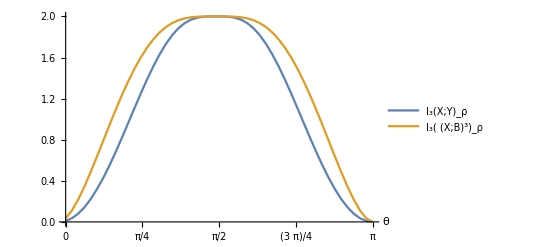

```mathematica
ListPlot[{IXYθ,IXBθ},DataRange->{0,Pi}, Joined->True,PlotLegends->{Label2,Label1},AxesLabel->{Style[θ, Medium]},Ticks->{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}]
```

```mathematica
Export["Exercice2.pdf",%]
```

Exercice2.pdf

Side notes and improvements

Easier solution for H(Y)

Side note to the resolution of this problem, notice how it is easy to compute that H(Y) is 2, thus this problem can be solved numerically using one computation less than previously proposed. To do so, let

```mathematica
HYθ=2;
IXYθ=HYθ-HYcondXθ/Log[2];
ListPlot[{IXYθ,IXBθ},DataRange->{0,Pi}, Joined->True,PlotLegends->{Label2,Label1},AxesLabel->{Style[θ, Medium]},Ticks->{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}]
```

-Graphics-

Where one can see that the output graphic is the same.

Solution avoiding double computation of P(y|x;θ) (if the value of H(Y) is unknown)

Let us start from the definition of the post-channel state, here one would need to define an extra function

```mathematica
ρYtot[θ_]:={ρYcondX[θ],1/4*ρY[θ]};
```

which will allow for computation of the different values needed at the same time (without needing to repeat the calculus of the function F presented before). Now let us move to the next step, the definition of the computation of the mutual information. This can be done as follows, where the eigenvalues are treated all at once, and just separated at the last step for the final computation

```mathematica
eigen2[θ_]:=Select[#,#>10^(-10)&]&/@{ρYtot[θ][[1]],ρYtot[θ][[2]]};
totaleigen2[θ_]:=eigen2[θ]*(Log[#]&/@eigen2[θ]);
IXY[θ_]:=-Tr[totaleigen2[θ][[2]]]+1/4*Tr[totaleigen2[θ][[1]]];
```

next just by adding this structure seen before

```mathematica
IXYθ=IXY[#]&/@Table[Pi* i/nn,{i,nn}]/Log[2];
ListPlot[{IXYθ,IXBθ},DataRange->{0,Pi}, Joined->True,PlotLegends->{Label2,Label1},AxesLabel->{Style[θ, Medium]},Ticks->{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}]
```

-Graphics-

However it ends up being much more inefficient, at least for the purpose of this exercise.

Problem 3

Starting by computing an string for the values functions presented at the beginning, plotting the results is trivial.

```mathematica
IXY1θ=N[IXY1[#]&/@Table[Pi* i/nn,{i,nn}]];
IXB1θ=N[IXB1[#]&/@Table[Pi* i/nn,{i,nn}]];
```

```mathematica
Label3=Subscript["I_3(X;Y)SubscriptBox[\\ ,\"ρ\"]-3I(X;Y)", "ρ"];
Label4="\!\(\*SubscriptBox[\(I\), \(3\)]\)( \!\(\*TemplateBox[{RowBox[{\"X\", \";\", \"B\"}], \"3\"},\"Superscript\"]\))\!\(\*SubscriptBox[\(\\ \), \(ρ\)]\)-3I(X;B)";
```

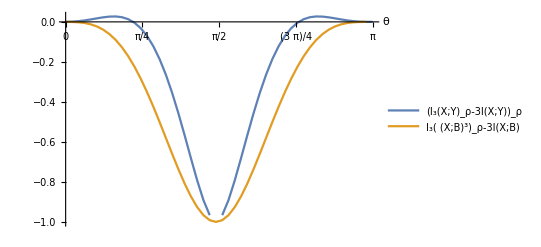

```mathematica
ListPlot[{IXYθ-3IXY1θ,IXBθ-3IXB1θ},DataRange->{0,Pi}, Joined->True,PlotLegends->{Label3,Label4},AxesLabel->{Style[θ, Medium]},Ticks->{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}]
```

```mathematica
Export["Exercice3.pdf",%]
```

Exercice3.pdf

Finally the whole document is exported

```mathematica
Export["mynotebook.pdf",EvaluationNotebook[]]
```

mynotebook.pdf